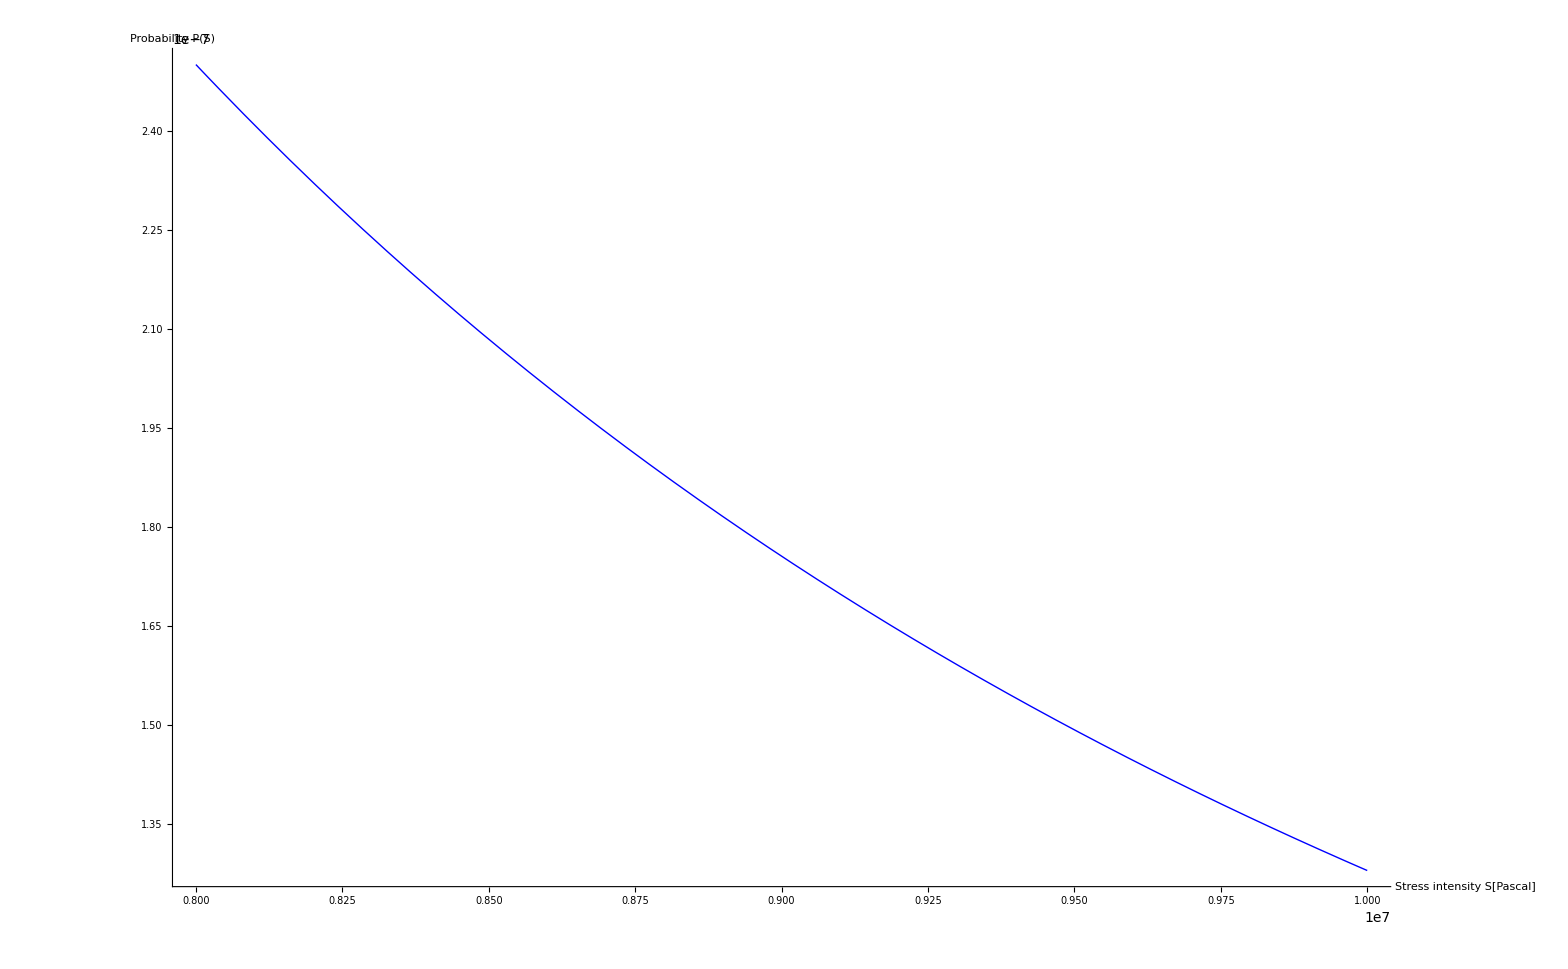

```mathematica
beta=3;
Smax=8000000;
c=(beta -1)*(Smax^(beta-1));
p=c*s^-beta;
Plot[p,{s,Smax,10000000},TicksStyle->Directive[Black,22],AxesStyle->Thick,AxesLabel->{Style["Stress intensity S[Pascal]",Black,24],Style["Probability P(S)",Black,24]},PlotStyle->{Blue,Thick}]
```